## Training Net

### Jacobian

Helpers to compute the Jacobian (of a function at a point)

```mathematica
(* Takes input of and outputs a Jacobian and a corresponding function*)
JacobianNet[func_, epsilon_:1*^-3]:= Module[
	{n, lin, net1, sharedFunc = NetInsertSharedArrays[func]}, 
	n = NetExtract[sharedFunc, "Input"];
	net1 = NetGraph[{ReplicateLayer[n], ConstantArrayLayer["Array" -> N[epsilon]*IdentityMatrix[n]], TotalLayer[]},{{1, 2} -> 3}];
	NetGraph[<|
		"addEpsilon"-> net1,
		"MapFunction" -> NetMapOperator[sharedFunc],
		"Function" -> sharedFunc,
		"subtract" -> NetMapThreadOperator[
			ThreadingLayer[Subtract,"Inputs"->2],<|"1"->1|>],
			"divideByEps" -> ElementwiseLayer[# / epsilon &],
			"transpose" -> TransposeLayer[]
		|>,
		{
			"addEpsilon" -> "MapFunction",
			{"MapFunction","Function"}->"subtract" -> "divideByEps" -> "transpose",
			"Function" -> NetPort["z"]
		}] 
];


Print[Style["JacobianNet Sanity Check:","Text"]];
W = ({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})/10.; b = {1,4,5}/10.;
<|
	"JacobianNet" -> MatrixForm @ Echo[JacobianNet[NetChain[{LinearLayer[3,"Input"->3, "Weights"->W,"Biases"->b], Tanh}]]][{-1,-2,-3}, "Output"],
	"Reference" -> MatrixForm @ N @ D[Tanh[(W.{x,y,z}+b)], {{x,y,z}}] /. {x->-1, y->-2, z->-3}
|>
```

JacobianNet Sanity Check:

NetGraph[<>]

<|JacobianNet→(0.0257492 | 0.0514984 | 0.0772476
0.00584126 | 0.00733137 | 0.00876188
0.000357628 | 0.000417233 | 0.000476837),Reference→(0.0257433 | 0.0514866 | 0.07723
0.00587307 | 0.00734133 | 0.0088096
0.000345462 | 0.000394814 | 0.000444166)|>

### LogDet

Helper to compute the LogDet (of a matrix):

```mathematica
(* 
Input:
n: dimension (Jacobian is nxn)
k: number of power series
Output:

*)
LogDetNet[n_,  k_:5] := Module[{powers, parts, elementwise, chains, diagonalElements, trace},

	(* (1) Find the power series expansion of log of the matrix *)
	(* Create k powers of the matrix *)
	powers = NetGraph[
		{ReplicateLayer[k-1], NetFoldOperator[DotLayer["Inputs" -> {{n, n}, {n, n}}], {"Output" -> "1"}],PrependLayer[]},
		{1 -> 2, NetPort["Input"] -> NetPort[2, "1"], {2, NetPort["Input"]} -> 3}
	];
	parts = Table[PartLayer[i], {i, 1, k}];
	(* Combine powers of Jacobian with the coefficients of power series of log*)
	elementwise = Table[ElementwiseLayer[#/(i*(-1)^(i+1)) &], {i, 1, k}];
	chains = NetChain /@ Transpose[{parts, elementwise}];
	(* Sum the powers and combine with the corresponding coefficients to get the power series expansion *)
	powers = NetGraph[Join[chains, {powers, TotalLayer[]}], {k + 1 -> Range[k], Range[k] -> k+2}];
	
	(* (2) Take the trace of the power series*)
	diagonalElements = Table[PartLayer[{i, i}], {i, 1, n}];
	trace = NetGraph[Join[diagonalElements, {TotalLayer[]}], {Range[n] -> n+1}, "Input" -> {n, n}];
	NetChain[{ConstantPlusLayer["Biases" -> -IdentityMatrix[n]],powers,trace}]
];
ExactLogDetNet[2] := NetGraph[
	{PartLayer[{1, 1}], PartLayer[{2, 2}],  PartLayer[{1, 2}], PartLayer[{2, 1}],
	ThreadingLayer[#1*#2 - #3*#4 &], 
	ElementwiseLayer[Log@*Abs]},
	{{1, 2, 3, 4} -> 5 -> 6},
	"Input" -> {2, 2}
];

Print[Style["LogDetNet Sanity Check:","Text"]];
jacob = {{3,-2},{-4,6}}/100.;
Echo[LogDetNet[2,3]];
<|
	"Reference (LogDet)" -> N @ Log @ Det @ jacob, "Reference (TraceLog)" -> N @ Tr @ MatrixLog[jacob],
	"ExactLogDetNet" -> ExactLogDetNet[2][jacob],
	Sequence @@ Map["LogDetNet["<>ToString[#]<>"]" -> LogDetNet[2,#][jacob]&, {15, 5, 3}]
|>
```

LogDetNet Sanity Check:

NetChain[<>]

<|Reference (LogDet)→-6.90776,Reference (TraceLog)→-6.90776,ExactLogDetNet→-6.90776,LogDetNet[15]→-5.54764,LogDetNet[5]→-4.14568,LogDetNet[3]→-3.40566|>

### Loss Function

-Graphics-

```mathematica
iResNetTrainingNet[forward_] := With[{
	n = Length[NetExtract[JacobianNet[forward],"Output"]]
	},
	NetGraph[<|
		"Jacobian" -> JacobianNet[forward],
		"LogDet" -> If[n == 2, ExactLogDetNet[n], LogDetNet[n]],
		"norm" -> DotLayer[],
		"subtract" -> ThreadingLayer[0.5 * #1 - #2&]
	|>,
		{NetPort[{"Jacobian", "Output"}] -> "LogDet",
		{NetPort[{"Jacobian", "z"}], NetPort[{"Jacobian", "z"}]} -> "norm",
		{"norm", "LogDet"} -> "subtract" -> NetPort["Loss"]}
	]
]

Print[Style["Example:","Text"]];
wrapInResidual[net_] := NetGraph[{net,TotalLayer[]},{{NetPort["Input"],1}->2}]
forward = NetChain[Table[wrapInResidual[NetChain[{2,ElementwiseLayer["ELU"],DropoutLayer[]}]], 3]]
iResNetTrainingNet[forward]
```

Example:

NetChain[<>]

NetGraph[<>]

### Normalization of the weights to satisfy Lipschitz constraint

-Graphics-

-Graphics--Graphics-

```mathematica
normalizeWeights[inputshape_, constant_] := NetGraph[
	<|
		"square" -> ElementwiseLayer[#^2&],
		"sum" -> SummationLayer[],
		"replicate" -> ReplicateLayer[inputshape],
		"divide" -> ThreadingLayer[#1*constant/Sqrt[#2]&]
	|>,
	{{NetPort["Input"], NetPort["Input"] -> "square" -> "sum" -> "replicate"} -> "divide"},
	"Input" -> inputshape
];

constrainedLinearLayer[inputsize_, outputsize_, constant_:0.5] := NetGraph[
	<|
		"Weights&Biases" -> ConstantArrayLayer["Output" -> {inputsize+1,outputsize}],
		"normalize" -> normalizeWeights[{inputsize+1,outputsize}, constant],
		"Weights" -> PartLayer[{1;;inputsize, All}],
		"Biases" -> PartLayer[{1,All}],
		"dot" -> DotLayer[],
		"plus" -> Plus
	|>,
	{"Weights&Biases" -> "normalize" -> {"Weights", "Biases"},
	{{NetPort["Input"], "Weights"} -> "dot", "Biases"} -> "plus"},
	"Input" -> inputsize
];

constrainedLinearLayer[2,2]
```

NetGraph[<>]

This helps to invert, but do not train well (underfit).

### Inversion of ResNet

-Graphics-

```mathematica
residualBlock[net_] := NetGraph[{net,TotalLayer[]},{{NetPort["Input"],1}->2}]

invertResidualNetwork[net_, iter_:10] := Module[
	{functions, invcores},
	functions = NetExtract[net, {All, 1}];
	invcores = NetGraph[
		{#, ThreadingLayer[Subtract]},
		{NetPort["State"] -> 1, NetPort["Input"] -> NetPort[2, 1], 1 -> NetPort[2, 2]}
	] & /@ functions;
	invcores = NetFoldOperator[#, {"Output" -> "State"}] & /@ invcores;
	invcores = NetGraph[{ReplicateLayer[iter], #, SequenceLastLayer[]},{1 -> 2 -> 3, NetPort["Input"] -> NetPort[2, "State"]}] & /@ invcores;
	NetChain @ Reverse[invcores]
];

Print[Style["Net Inversion Sanity Check:","Text"]];

in = {0.2, -0.3};

forward = NetInitialize[NetChain[Table[residualBlock[NetChain[{2,ElementwiseLayer[Erf]}]], 5]], RandomSeeding->5]
in -> invertResidualNetwork[forward, 10] @ forward @ in

forward2 = NetInitialize[NetChain[Table[residualBlock[NetChain[{constrainedLinearLayer[2,2],ElementwiseLayer[Erf]}]], 5]], RandomSeeding->5]
in -> invertResidualNetwork[forward2, 10] @ forward2 @ in
```

Net Inversion Sanity Check:

NetChain[<>]

{0.2,-0.3}→{0.200623,-0.300393}

NetChain[<>]

{0.2,-0.3}→{0.2,-0.3}

## Experiments

### Data (“Two Moons”)

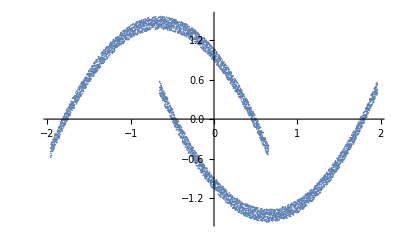

```mathematica
points=5000;
noise=0.1;
k=4/(points-2);
SeedRandom[1969];
data=Standardize[Join[Table[{x,-2(x+0.5)^2+1.5+RandomReal[{-noise,noise}]},{x,-1.5,0.5,k}],Table[{x,2(x-0.5)^2-1.5+RandomReal[{-noise,noise}]},{x,-0.5,1.5,k}]]];
ListPlot[data]
```

#### Data normalization

The data is already normalized. Let’s ignore this step for now.

```mathematica
Mean[data]
StandardDeviation[data]
```

{-6.31495×10^-17,-3.2192×10^-16}

{1.,1.}

### Train

NetChain[<>]

NetGraph[<>]

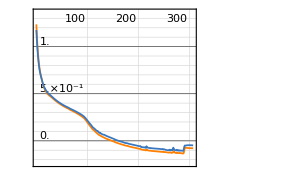
NetTrain Results
summary | ,,  batches:19341  rounds:307  time:26s  examples/s:47931
data | ,,  training examples:4032  validation examples:1024  processed examples:1237824  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:-7.89×10^-2
validation | ,,  loss:-4.81×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

NetChain[<>]

```mathematica
forward = NetChain[Table[residualBlock[NetChain[{2, ElementwiseLayer[0.5*Tanh[#]&]}]], 5]]
traininnet = iResNetTrainingNet[forward]

trainingresult = NetTrain[
	traininnet,
	<|"Input" -> data|>,
	All,
	ValidationSet->Scaled[0.2],
	LearningRateMultipliers -> {{"Jacobian", "addEpsilon"}->None},
	Method -> {"ADAM"(*, "L2Regularization" -> 0.01*)},
	TrainingStoppingCriterion -> <|"Criterion"->"Loss", "Patience"->20|>, MaxTrainingRounds->1*^10,
	RandomSeeding -> 51
]
trainednet = NetExtract[trainingresult["TrainedNet"], {"Jacobian", "Function"}]
```

### Test the train model

#### Check Inversion

```mathematica
in = {1, -1.5};
With[{inverse = invertResidualNetwork[trainednet,10]},
	AssociationMap[inverse[trainednet[#]]&,
		{{1, -1.5}, {2,0},{-1, 1.5}, {-2,0},{0,0}}
	]
]
```

<|{1,-1.5}→{0.999999,-1.50024},{2,0}→{1.98724,0.0134239},{-1,1.5}→{-1.,1.49998},{-2,0}→{-1.99172,-0.011116},{0,0}→{-1.28238,-0.401369}|>

#### Generate random samples

Original data:

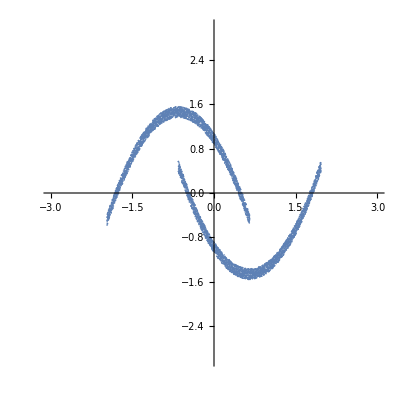

Latent data (should be close to Gaussian):

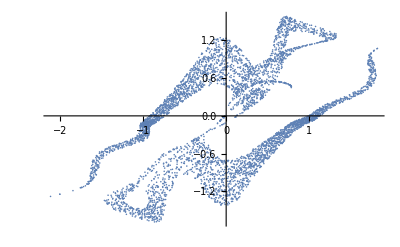

Generated data (with inverse network):

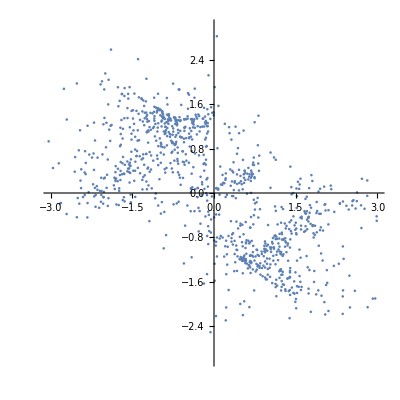
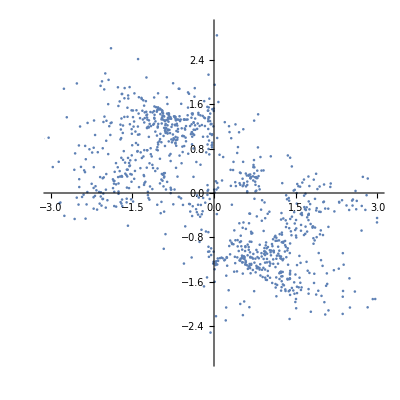
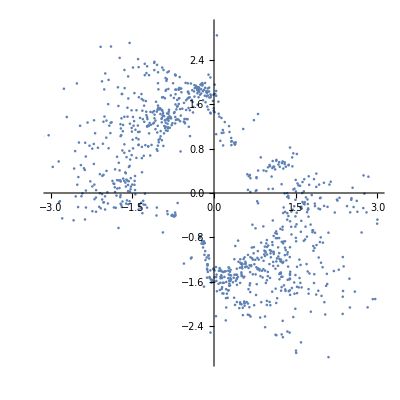
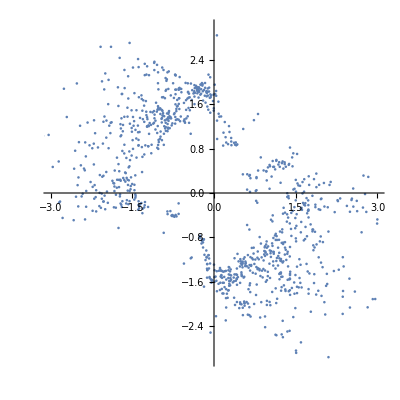
3→-Graphics-
5→-Graphics-
10→-Graphics-
50→-Graphics-

```mathematica
Print[Style["Original data:", "Text"]];
$plotargs = Sequence[PlotRange -> {{-3,3},{-3,3}},AspectRatio->Automatic];
ListPlot[data, $plotargs]

Print[Style["Latent data (should be close to Gaussian):", "Text"]];
ListPlot[trainednet@data]

Print[Style["Generated data (with inverse network):", "Text"]];
zdata = RandomVariate[NormalDistribution[0,1],{1000,2}];
AssociationMap[ListPlot[invertResidualNetwork[trainednet,#][zdata], $plotargs]&, {3, 5, 10, 50}] // Normal // Column
```